```mathematica
(* angle w.r.t. x-axis *)
```

```mathematica
ArcTan[0.5]*180/Pi
```

26.5651

```mathematica
(* Set x_{||} as parallel to kvec and field components perp and parallel to kvec *)
```

```mathematica
xpar=x*Cos[a]+y*Sin[a]
Bperp=Bperp0*Sin[2*Pi*xpar]
Bpar=Bpar0
```

x Cos[a]+y Sin[a]

Bperp0 Sin[2 π (x Cos[a]+y Sin[a])]

Bpar0

```mathematica
(* Set velocity relative to kvec *)
```

```mathematica
Vperp=Vperp0*Sin[2*Pi*xpar]
Vpar=Vpar0
```

Vperp0 Sin[2 π (x Cos[a]+y Sin[a])]

Vpar0

```mathematica
(* Solve for Vx and Vy *)
```

```mathematica
eq1=Vperp==Vy*Cos[a]-Vx*Sin[a]
eq2=Vpar==Vx*Cos[a]+Vy*Sin[a]
sols=FullSimplify[Solve[{eq1,eq2},{Vx,Vy}]]
myVx=sols[[1,1,2]]
myVy=sols[[1,2,2]]
```

Vperp0 Sin[2 π (x Cos[a]+y Sin[a])]==Vy Cos[a]-Vx Sin[a]

Vpar0==Vx Cos[a]+Vy Sin[a]

{{Vx→Vpar0 Cos[a]-Vperp0 Sin[a] Sin[2 π (x Cos[a]+y Sin[a])],Vy→Vpar0 Sin[a]+Vperp0 Cos[a] Sin[2 π (x Cos[a]+y Sin[a])]}}

Vpar0 Cos[a]-Vperp0 Sin[a] Sin[2 π (x Cos[a]+y Sin[a])]

Vpar0 Sin[a]+Vperp0 Cos[a] Sin[2 π (x Cos[a]+y Sin[a])]

```mathematica
(* now get field *)
```

```mathematica
eq1=Bperp==By*Cos[a]-Bx*Sin[a]
eq2=Bpar==Bx*Cos[a]+By*Sin[a]
sols=FullSimplify[Solve[{eq1,eq2},{Bx,By}]]
myBx=sols[[1,1,2]]
myBy=sols[[1,2,2]]
```

Bperp0 Sin[2 π (x Cos[a]+y Sin[a])]==By Cos[a]-Bx Sin[a]

Bpar0==Bx Cos[a]+By Sin[a]

{{Bx→Bpar0 Cos[a]-Bperp0 Sin[a] Sin[2 π (x Cos[a]+y Sin[a])],By→Bpar0 Sin[a]+Bperp0 Cos[a] Sin[2 π (x Cos[a]+y Sin[a])]}}

Bpar0 Cos[a]-Bperp0 Sin[a] Sin[2 π (x Cos[a]+y Sin[a])]

Bpar0 Sin[a]+Bperp0 Cos[a] Sin[2 π (x Cos[a]+y Sin[a])]

```mathematica
(* check *)
```

```mathematica
myBx//.{a->0}
myBy//.{a->0}
```

Bpar0

Bperp0 Sin[2 π x]

```mathematica
(* check divb *)
```

```mathematica
divb=D[myBx,x]+D[myBy,y]
```

0

```mathematica
myBx
Integrate[myBx,y]
```

Bpar0 Cos[a]-Bperp0 Sin[a] Sin[2 π (x Cos[a]+y Sin[a])]

Bpar0 y Cos[a]+(Bperp0 Cos[2 π (x Cos[a]+y Sin[a])])/(2 π)

```mathematica
(* get vector potential *)
```

```mathematica
Az1=Integrate[-myBy,x]+F[y]
Az2=Integrate[myBx,y]+G[x]
Aeq1=FullSimplify[D[Az2,x]-(-myBy)]
Aeq2=FullSimplify[D[Az1,y]-(myBx)]
myG=DSolve[Aeq1==0,G[x],x]
myF=DSolve[Aeq2==0,F[y],y]
finalA1=Az1//.myF[[1]]
finalA2=Az2//.myG[[1]]
FullSimplify[finalA1-finalA2]
```

(Bperp0 Cos[2 π (x Cos[a]+y Sin[a])])/(2 π)+F[y]-Bpar0 x Sin[a]

Bpar0 y Cos[a]+(Bperp0 Cos[2 π (x Cos[a]+y Sin[a])])/(2 π)+G[x]

Bpar0 Sin[a]+G'[x]

-Bpar0 Cos[a]+F'[y]

{{G[x]→C[1]-Bpar0 x Sin[a]}}

{{F[y]→C[1]+Bpar0 y Cos[a]}}

C[1]+Bpar0 y Cos[a]+(Bperp0 Cos[2 π (x Cos[a]+y Sin[a])])/(2 π)-Bpar0 x Sin[a]

C[1]+Bpar0 y Cos[a]+(Bperp0 Cos[2 π (x Cos[a]+y Sin[a])])/(2 π)-Bpar0 x Sin[a]

0

```mathematica
(* so good solution for vector potential *)
```

```mathematica
FullSimplify[finalA1]
```

C[1]+Bpar0 y Cos[a]+(Bperp0 Cos[2 π (x Cos[a]+y Sin[a])])/(2 π)-Bpar0 x Sin[a]

```mathematica
(* get Bz *)
```

```mathematica
(* check potential *)
```

```mathematica
FullSimplify[D[finalA1,y]-myBx]
FullSimplify[D[finalA1,x]-(-myBy)]
```

0

0

```mathematica
Bz=Bz0*Cos[2*Pi*xpar]
Ax=Integrate[-Bz,y]+F[x]
Ay=Integrate[Bz,x]+G[y]
```

Bz0 Cos[2 π (x Cos[a]+y Sin[a])]

F[x]-(Bz0 Csc[a] Sin[2 π (x Cos[a]+y Sin[a])])/(2 π)

G[y]+(Bz0 Sec[a] Sin[2 π (x Cos[a]+y Sin[a])])/(2 π)

```mathematica
(* Choose $a$ *)
```

```mathematica
1/Csc[a]
```

Sin[a]

```mathematica
mya={a->ArcTan[2]}
```

{a→ArcTan[2]}

```mathematica
(* For given $a$ get Lx *)
```

```mathematica
Bz1=Bz//.{Bz0->0.1,x->0,y->0}//.mya
Bz2=Bz//.{Bz0->0.1,x->0,y->Lx/2}//.mya
Bz3=Bz//.{Bz0->0.1,x->Lx,y->0}//.mya
Bz4=Bz//.{Bz0->0.1,x->Lx,y->Lx/2}//.mya
theLx=FindRoot[{Bz4==Bz3},{Lx,2},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->25]
otherLx=Solve[Bz4==Bz3,Lx]
(*mya=FindRoot[{Bz1==Bz2,Bz3==Bz4},{a,0.6},{Lx,2}]*)
```

0.1

0.1 Cos[(2 Lx π)/(√5)]

0.1 Cos[(2 Lx π)/(√5)]

0.1 Cos[(4 Lx π)/(√5)]

FindRoot::precw: The precision of the argument function ({0.1\ Cos[4\ Lx\ π/√5] == 0.1\ Cos[2\ Lx\ π/√5]}) is less than WorkingPrecision (25.).

{Lx→2.236067977499711300649514}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Lx→-2.23607},{Lx→-1.49071},{Lx→-0.745356},{Lx→0.},{Lx→0.745356},{Lx→1.49071},{Lx→2.23607}}

```mathematica
(* Get accurate version *)
```

```mathematica
finalLx=N[theLx,16]
fromFindRoot=finalLx
CForm[finalLx[[1,2]]]
```

{Lx→2.23606797749971}

{Lx→2.23606797749971}

2.236067977499711

```mathematica
N[Sqrt[5],16]
```

2.23606797749979

```mathematica
(* Some plots of this solution with this $a$ and this $Lx$ *)
```

1.11803

2.23607

0.1 Cos[2 π (x/(√5)+(2 y)/(√5))]

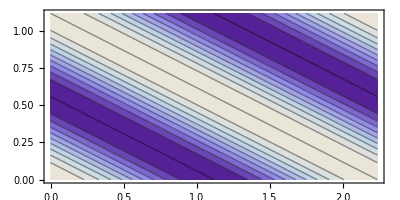

```mathematica
(*finalLx=theLx[[9]]*)
myLy=(Lx/2)//.finalLx
myLx=Lx//.finalLx
it=Bz//.mya//.{Bpar0->1,Bperp0->0.1,Bz0->0.1}
ContourPlot[it,{x,0,myLx},{y,0,myLy},AspectRatio->1/2]
```

```mathematica
Bp=FullSimplify[Sqrt[myBx^2+myBy^2]]//.{Bpar0->0,Bperp0->0.1}//.mya[[1]]
```

(√(0.01-0.01 Cos[4 π (x/(√5)+(2 y)/(√5))]))/(√2)

```mathematica
FullSimplify[Sqrt[myBx^2+myBy^2],{Bpar0>0,Bperp0>0}]
```

(√(2 Bpar0^2+Bperp0^2-Bperp0^2 Cos[4 π (x Cos[a]+y Sin[a])]))/(√2)

(√(201/100-1/100 Cos[4 π (x/(√5)+(2 y)/(√5))]))/(√2)

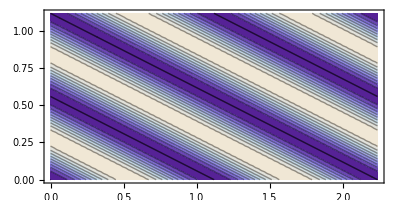

{1.00499,{x→0.559017,y→-1.09457×10^-8}}

```mathematica
(* Toth says pressure should be constant, so check *)
Bp=FullSimplify[Sqrt[myBx^2+myBy^2]]//.mya[[1]]//.{Bperp0->1/10,Bz0->1/10,Bpar0->1}
ContourPlot[Bp,{x,0,myLx},{y,0,myLy},AspectRatio->1/2]
FindMaximum[Bp,{x,0,myLx},{y,0,myLy}]
```

```mathematica
Bp//.{x->0.5590170143128042,y->-1.0945650226311522*^-8}
```

1.00499

(√101)/10

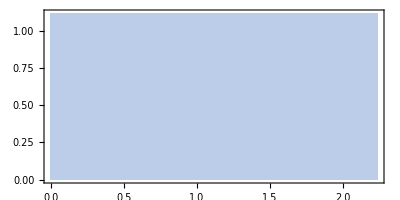

```mathematica
pressure=FullSimplify[Sqrt[myBx^2+myBy^2+Bz^2]]//.mya[[1]]//.{Bperp0->1/10,Bz0->1/10,Bpar0->1}
ContourPlot[pressure,{x,0,myLx},{y,0,myLy},AspectRatio->1/2]
```

```mathematica
(* runtime tf *)
```

```mathematica
alpha0=ArcTan[2]
NL1=Lx/Sin[alpha0]//.fromFindRoot
```

ArcTan[2]

2.5

```mathematica
Ly*Sqrt[5]//.{Ly->Lx/2}//.fromFindRoot
```

2.5

```mathematica
alpha0=ArcTan[2]
time=5*myLx/(2.0*Sin[alpha0])
```

ArcTan[2]

6.25